```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];
(*Latex dictionary*)
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[th1]:=Subscript[θ,1];Format[th2]:=Subscript[θ,2];Format[thv]:=Subscript[θ,v];
Format[th]:=θ;
Format[Las]:=Subscript[Λ,s];Format[Lav]:=Subscript[Λ,v];Format[be1]:=Subscript[β,1];Format[be2]:=Subscript[β,2];
(*Format[al1]:=Subscript[α,1];Format[al2]:=Subscript[α,2];*)Format[siv]:=Subscript[σ,v];
Format[si1]:=Subscript[σ,1];Format[si2]:=Subscript[σ,2];
Format[et1]:=Subscript[η,1];Format[et2]:=Subscript[η,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[y1]:=Subscript[y,1];Format[y2]:=Subscript[y,2];
Format[r1]:=Subscript[r,1];Format[r2]:=Subscript[r,2];
Format[c1]:=Subscript[c,1];Format[c2]:=Subscript[c,2];
(*Two-Strain Model with vaccination*)RNc={"S"+"I1"->2  "I1", "I1"-> "C1", "C1"-> "R1", "R1"+  "Y2"->2  "Y2",
"S"+"I2" ->2  "I2", "I2"-> "C2", "C2"-> "R2", "R2"+ "Y1"->2"Y1",
"S"+"Y1" ->  "Y1"+  "I1","S"+"Y2" ->  "Y2"+ "I2",
 "R1"+  "I2"-> "I2"+  "Y2", "R2"+"I1"->"I1"+"Y1","V"->"Z","Z"+"Y2"-> 2"Y2",
 "Z"+ "I2"->  "I2"+  "Y2", "Y2"->"R", "Y1"->"R"};
RN=Join[{0->"S",0->"V"},RNc,
{"S"->0,"I1" ->0,"C1" ->0,"R1" ->0,"Y2" ->0,"I2" ->0,"C2" ->0,"R2" ->0,"Y1" ->0,"V"->0,"Z"->0,"R"->0}];
ks={ Las,Lav,be1,ga1,th1,si2 be2,be2,ga2,th2,si1 be1,be1,be2,si2 be2,si1 be1,
thv,siv be2,siv be2,ga2,ga1,mu,mu,mu,
mu,mu,mu,mu,mu,mu,mu,mu,mu};rts=mRts[RN,ks]
rts//Length
```

mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,S+Y1→I1+Y1,S+Y2→I2+Y2,I2+R1→I2+Y2,I1+R2→I1+Y1,V→Z,Y2+Z→2 Y2,I2+Z→I2+Y2,Y2→R,Y1→R,S→0,I1→0,C1→0,R1→0,Y2→0,I2→0,C2→0,R2→0,Y1→0,V→0,Z→0,R→0},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,β_1,β_2,β_2 σ_2,β_1 σ_1,θ_v,β_2 σ_v,β_2 σ_v,γ_2,γ_1,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ}]

2

```mathematica
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
```

Transpose::nmtx: The first two levels of {{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,«21»}]} cannot be transposed.

reactions and transitions: Transpose[{{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,S+Y1→I1+Y1,S+Y2→I2+Y2,I2+R1→I2+Y2,I1+R2→I1+Y1,V→Z,Y2+Z→2 Y2,I2+Z→I2+Y2,Y2→R,Y1→R,S→0,I1→0,C1→0,R1→0,Y2→0,I2→0,C2→0,R2→0,Y1→0,V→0,Z→0,R→0},mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,S+Y1→I1+Y1,S+Y2→I2+Y2,I2+R1→I2+Y2,I1+R2→I1+Y1,V→Z,Y2+Z→2 Y2,I2+Z→I2+Y2,Y2→R,Y1→R,S→0,I1→0,C1→0,R1→0,Y2→0,I2→0,C2→0,R2→0,Y1→0,V→0,Z→0,R→0},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,β_1,β_2,β_2 σ_2,β_1 σ_1,θ_v,β_2 σ_v,β_2 σ_v,γ_2,γ_1,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ}]}]

```mathematica
(*Get bdAn outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,R0A,EA,E1t,E2t} = bdAn[RN, rts];
Print["R1,R2 are"]
{R01,R02}=R0A/.E0
```

Transpose::nmtx: The first two levels of {{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,«21»}]} cannot be transposed.

reactions and transitions: Transpose[{{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,S+Y1→I1+Y1,S+Y2→I2+Y2,I2+R1→I2+Y2,I1+R2→I1+Y1,V→Z,Y2+Z→2 Y2,I2+Z→I2+Y2,Y2→R,Y1→R,S→0,I1→0,C1→0,R1→0,Y2→0,I2→0,C2→0,R2→0,Y1→0,V→0,Z→0,R→0},mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,S+Y1→I1+Y1,S+Y2→I2+Y2,I2+R1→I2+Y2,I1+R2→I1+Y1,V→Z,Y2+Z→2 Y2,I2+Z→I2+Y2,Y2→R,Y1→R,S→0,I1→0,C1→0,R1→0,Y2→0,I2→0,C2→0,R2→0,Y1→0,V→0,Z→0,R→0},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,β_1,β_2,β_2 σ_2,β_1 σ_1,θ_v,β_2 σ_v,β_2 σ_v,γ_2,γ_1,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ,μ}]}]

Set::shape: Lists {RHS,var,par,cp,mSi,Jx,Jy,E0,ngm,R0,«4»} and bdAn[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},mRts[{0→S,0→V,I1+S→2 I1,I1→C1,C1→R1,R1+Y2→2 Y2,I2+S→2 I2,I2→C2,C2→R2,R2+Y1→2 Y1,«21»},{Λ_s,Λ_v,β_1,γ_1,θ_1,β_2 σ_2,β_2,γ_2,θ_2,β_1 σ_1,«21»}]] are not the same shape.

R1,R2 are

ReplaceAll::reps: {E0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {R01,R02} and R0A/.E0 are not the same shape.

R0A/.E0

```mathematica
{E1,E2,R12,R21,coP,fl}=invN[E1t,E2t,R0A,E0,par,cp,2,4]
```

Selected E1 (solution 2)

Selected E2 (solution 4)

E2 numerical: {C1→0.,C2→0.0546487,I2→0.117262,R→0.0531447,R1→0.,R2→0.0504321,S→0.811499,V→0.48869,Y2→0.0593054,Z→0.424832}

coP: {β_1→2.98909,β_2→1.51156,γ_1→1.07542,γ_2→0.872902,Λ_s→1.00706,Λ_v→0.99939,μ→0.974091,σ_1→0.903798,σ_2→3.0242,σ_v→0.966066,θ_1→0.945214,θ_2→0.898931,θ_v→1.07095}

R12,R21: {1.2086,1.25}

R01,R02: {1.5078,1.27087}

```mathematica
(*eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]
p0val=par/.coP;
pos=fpHopf[RHS, var, par, p0val]*)
```

Auto-determined varInd: {1,3,6}

Susceptible: S

Strain 1 (first compartment): I1

Strain 2 (first compartment): Y2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: β_1 = 1.98242, β_2 = 1.18939

Adjusted ranges: β_1 ∈ [0.001, 5.97818], β_2 ∈ [0.001, 3.02311]

Scanning 121 parameter combinations...

Checked 30 potential coexistence points

All Rij equations: {0.504434 β_1==1,0.840767 β_2==1,(0.0690938 (3.50924+10.3983 β_1) β_2)/β_1==1,-1/β_20.564822 β_1 (-0.634221+15.1758 β_2-2.75027 √(0.946947 (3.70527-3.11527 β_2) β_2+(-0.230603+5.84265 β_2)^2))==1}

DFE: 16 (13%)

E2: 40 (33%)

E1: 35 (29%)

EE-Stable: 30 (25%)

{0.78125,Null}

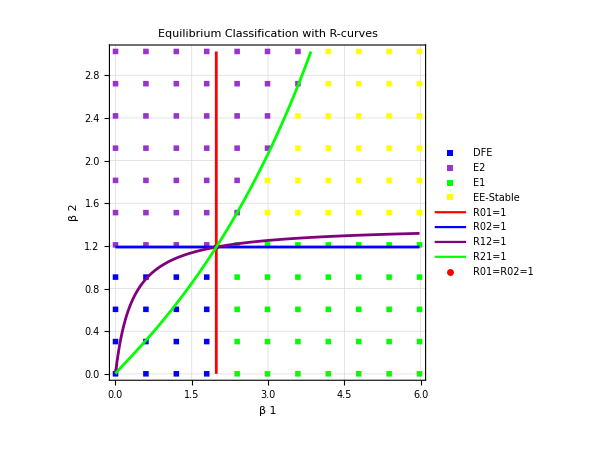

```mathematica
plotInd={1,2};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);

(*Call scan using all the precomputed values from memory*)
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]

fPl
```

```mathematica
Export["BulhScan.pdf",fPl]
```

RahmanScan.pdf